Try cylindrical geom

```mathematica
normFac[vbNormW_,kappa_]:=2/π^(1/2)(1/2(kappa^(3/2)Gamma[kappa-1/2])/Gamma[kappa+1]+vbNormW/(√π)Hypergeometric2F1[1/2,kappa,3/2,-vbNormW^2/kappa])^-1
func[rho_,phi_,vb_,kappa_,w_,b_]:=(1+(rho^2+vb^2-2 vb rho (1 - (Sin[phi])^2 b)^(1/2))/(kappa w))^(-(kappa+1))
```

```mathematica
funcNoW[rho_,phi_,vb_,kappa_,b_]:=normFac[vb,kappa](1+(rho^2+vb^2-2 vb rho (1 - (Sin[phi])^2 b)^(1/2))/kappa)^(-(kappa+1))
```

#### The cylindrical-coord version of the Barbosa func, in terms of bulk velocity v_(b,th) = v_b/v_th=√(ΔΦ/(k T)) normalized by the thermal velocity v_th= √(kT/m)(originates here, journal__20180125__somesing_work)

```mathematica
vbth[deltaPhi_,T_]:=√(deltaPhi/T);
```

```mathematica
normFacAlt[vbth_,kappa_]:=2/(π^(1/2)(kappa - 3/2)^(3/2))(1/2 Gamma[kappa-1/2]/Gamma[kappa+1]+vbth/(√π kappa(kappa-3/2)^(1/2))Hypergeometric2F1[1/2,kappa,3/2,-vbth^2/(kappa-3/2)])^-1;
funcAlt[rho_,phi_,vbth_,kappa_,b_]:=(1+(rho^2+vbth^2-2 vbth rho (1 - (Sin[phi])^2 b)^(1/2))/(kappa-3/2 ))^(-(kappa+1))
```

```mathematica
(*funcNoW[rho_,phi_,vb_,kappa_,b_]:=normFac[vb,kappa](1+(rho^2+vb^2-2 vb rho (1 - (Sin[phi])^2 b)^(1/2))/kappa)^(-(kappa+1))*)
```

```mathematica
barbDist[vpar_,vperp_,deltaPhi_,T_,alpha_]:=4/(π^(1/2)Erfc[-√(deltaPhi/T)])Exp[-1(vpar^2+vperp^2+deltaPhi/T-2 √(deltaPhi/T) (vpar^2+ vperp^2 (1 - alpha) )^(1/2))] UnitStep[vpar]
barbAsymp[deltaPhi_,T_]:=1+2(√(deltaPhi/T))/Erfc[-√(deltaPhi/T)] NIntegrate[Erfc[x],{x,-√(deltaPhi/T),∞}]
```

```mathematica
dPhi=941;Tm=110;
vb[kappa_]:=√(dPhi/(Tm(1-3/(2 kappa))))
vbAlt=√(dPhi/Tm);
```

```mathematica
b=1;
```

```mathematica
Table[NIntegrate[rho^2 Sin[phi]  funcNoW[rho,phi,vb[kaps],kaps,b],{rho,0,∞},{phi,0,π/2}],{kaps,{100,10,3,245/100,17/10,16/10}}]
```

{1.,1.,1.,1.,1.,1.}

```mathematica
Table[NIntegrate[rho^2 Sin[phi]  normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,b],{rho,0,∞},{phi,0,π/2}],{kaps,{100,10,3,245/100,17/10,16/10}}]
```

{1.,1.,1.,1.,1.,1.}

```mathematica
b=1/2;Table[NIntegrate[rho^2 Sin[phi] funcNoW[rho,phi,vb[kaps],kaps,b],{rho,0,∞},{phi,0,π/2},WorkingPrecision->12],{kaps,{500,10,3,245/100,17/10,16/10,155/100}}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{2.19045836236,2.17790312959,2.13236849267,2.11370991201,2.05437627352,2.03576262167,2.02242343411}

```mathematica
Table[NIntegrate[rho^2 Sin[phi]  normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,b],{rho,0,∞},{phi,0,π/2}],{kaps,{100,10,3,245/100,17/10,16/10}}]
```

{2.18963,2.17793,2.13239,2.1137,2.05438,2.03576}

```mathematica
NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,b],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10]
```

2.19067

```mathematica
b=1/5;
```

```mathematica
Table[NIntegrate[rho^2 Sin[phi] funcNoW[rho,phi,vb[kaps],kaps,b],{rho,0,∞},{phi,0,π/2},WorkingPrecision->12],{kaps,{500,10,3,245/100,17/10,16/10,155/100}}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{6.03487184887,5.94014854919,5.70761342457,5.62585425251,5.35243020685,5.24836374555,5.16477555738}

```mathematica
Table[NIntegrate[rho^2 Sin[phi]  normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,b],{rho,0,∞},{phi,0,π/2}],{kaps,{100,10,3,245/100,17/10,16/10}}]
```

{6.02717,5.94015,5.70761,5.62585,5.35226,5.24835}

```mathematica
NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,b],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10]
```

6.0368

```mathematica
b=1/6;
```

```mathematica
Table[NIntegrate[rho^2 Sin[phi]  normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,b],{rho,0,∞},{phi,0,π/2}],{kaps,{100,10,3,245/100,17/10,16/10}}]
```

{7.06551,7.00101,6.82003,6.75049,6.46907,6.34046}

```mathematica
NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,b],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10]
```

7.07257

```mathematica
b=1/7;
```

```mathematica
Table[NIntegrate[rho^2 Sin[phi]  normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,b],{rho,0,∞},{phi,0,π/2}],{kaps,{100,10,3,245/100,17/10,16/10}}]
```

{7.96637,7.94167,7.86571,7.82799,7.5856,7.4384}

```mathematica
NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,b],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10]
```

7.96905

```mathematica
b=1/8;
```

```mathematica
Table[NIntegrate[rho^2 Sin[phi]  normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,b],{rho,0,∞},{phi,0,π/2}],{kaps,{100,10,3,245/100,17/10,16/10}}]
```

{8.74755,8.77312,8.84214,8.85354,8.69819,8.5401}

```mathematica
NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,b],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10]
```

8.74485

```mathematica
b=1/9;
```

```mathematica
Table[NIntegrate[rho^2 Sin[phi]  normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,b],{rho,0,∞},{phi,0,π/2}],{kaps,{100,10,3,245/100,17/10,16/10}}]
```

{9.42741,9.50884,9.75067,9.82562,9.80394,9.64379}

```mathematica
NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,b],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10]
```

9.41883

```mathematica
b=1/10;
```

```mathematica
Table[NIntegrate[rho^2 Sin[phi]funcNoW[rho,phi,vb[kaps],kaps,b],{rho,0,∞},{phi,0,π/2},WorkingPrecision->15],{kaps,{500,10,3,245/100,17/10,16/10}}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{10.0105653620764,10.1618587500057,10.5946629512799,10.7447262819708,10.9005392450859,10.747974874593}

```mathematica
Table[NIntegrate[rho^2 Sin[phi]  normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,b],{rho,0,∞},{phi,0,π/2}],{kaps,{100,10,3,245/100,17/10,16/10}}]
```

{10.0223,10.1619,10.5947,10.7447,10.9005,10.748}

```mathematica
NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,b],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10]
```

10.0077

```mathematica
b=1/72;
```

```mathematica
Table[NIntegrate[rho^2 Sin[phi]  normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,b],{rho,0,∞},{phi,0,π/2}],{kaps,{100,10,3,245/100,17/10,16/10}}]
```

{16.7309,18.1272,24.6179,28.603,53.0122,65.4062}

```mathematica
65.4062/16.7309
```

3.90931

```mathematica
b=1/100;
```

```mathematica
Table[NIntegrate[rho^2 Sin[phi]  normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,b],{rho,0,∞},{phi,0,π/2}],{kaps,{100,10,3,245/100,17/10,16/10}}]
```

{17.149,18.6597,25.8666,30.4529,61.9795,81.3362}

```mathematica
NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,b],{vpar,0,∞},{vperp,0,∞},AccuracyGoal->10,PrecisionGoal->10]
```

17.0046

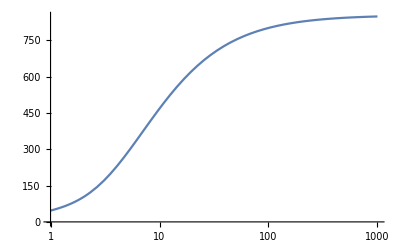

```mathematica
LogLinearPlot[NIntegrate[rho^2 Sin[phi]  normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],100,1/RB],{rho,0,∞},{phi,0,π/2}],{RB,1,1000}]
```

Old Parametric Plot

```mathematica
ParametricPlot3D[{rho Cos[phi],rho Sin[phi],normFac[vb[1.7],1.7]funcNoW[rho,phi,vb[1.7],1.7,0]},{rho,0,10},{phi,-π/2,π/2},PlotRange->All,ImageSize->900,PlotPoints->80]
```

-Graphics3D-